```mathematica
(*Include FEM tools*)
<<NDSolve`FEM`
(*@brief Find node Id
@param[in] (nodes) all the mesh nodes
@param[in] (coords) coords you need to find
@param[out] node Ids *)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
(*@brief Get Integration Points and Weights
@param[in] polinomial order (1 or 2)
@param[in] dimension
@param[out] Points and Weights *)
IntegrationRule[order_,dim_]:=Block[{pts,ws,npts,matpsts},
If[dim≠1&&dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==1,
pts=ElementIntegrationPoints[LineElement,order+1];
ws=ElementIntegrationWeights[LineElement,order+1];
matpsts=Table[{pts[[i]][[1]],0,0,ws[[i]]},{i,1,Length[ws]}];
];
If[dim==2,
pts=ElementIntegrationPoints[QuadElement,order+2];
ws=ElementIntegrationWeights[QuadElement,order+2];
matpsts=Table[{pts[[i]][[1]],pts[[i]][[2]],0,ws[[i]]},{i,1,Length[ws]}];
];
If[dim==3,
pts=ElementIntegrationPoints[HexahedronElement,order+3];
ws=ElementIntegrationWeights[HexahedronElement,order+3];
matpsts=Table[{pts[[i]][[1]],pts[[i]][[2]],pts[[i]][[3]],ws[[i]]},{i,1,Length[ws]}];
];
matpsts
];
(*@brief Compute 1D Shape Functions And Derivatives
@param[in] polinomial order (1 or 2)
@param[in] dimension
@param[out] Shape Functions And Derivatives *)
ComputeShape1D[order_,var_,x0_,xf_]:=Block[{npoints},npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf-x0) (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]]
(*@brief Compute Shape Functions And Derivatives
@param[in] polinomial order (1 or 2)
@param[in] dimension
@param[out] Shape Functions And Derivatives *)
ComputeShape[order_,dim_]:=Block[{psis,dpsis,zeta,xi,eta },
If[dim≠1&&dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==1,
psis=ElementShapeFunction[LineElement,order][xi];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
];
If[dim==2,
psis=ElementShapeFunction[QuadElement,order][xi,eta];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
];
If[dim==3,
psis=ElementShapeFunction[HexahedronElement,order][xi,eta,zeta];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta],D[psis[[i]],zeta]},{i,1,Length[psis]}]];
];
{psis,dpsis}
];
(*@brief Compute integration point contribution
@param[in] data(psis,GradPsi,elcoords,weight)
@param[in] random variables hhatv
@param[out] Element Contribution Matrix ek *)
Contribute[data_,dim_,hhatv_]:=Block[{randomdata,stress,NShapes,nusqr,pts,w,npts,matpsts,thick=tick,const,psis,GradPsi,Jac, nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight},
If[dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
{psis,GradPsi,elcoords,weight}=data;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
If[Length[hhatv]>1,
young=hhatv.psis;
];
If[dim==2,
B={
Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]
};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};
nusqr=nu nu;
C={{young/(1-nusqr),nu young/(1-nusqr),0},{nu young/(1-nusqr),young/(1-nusqr),0},{0,0,young/(2 (1+nu))}};
ek=thick(Transpose[B].C.B)weight DetJ;
(*sx,sy,sxy*)
stress={0,0,0};
,
B={
Flatten[Table[{GradPhi[[1,i]],0,0},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[2,i]],0},{i,1,nnodes}],1],
Flatten[Table[{0,0,GradPhi[[3,i]]},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[3,i]],GradPhi[[2,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[3,i]],0,GradPhi[[1,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]],0},{i,1,nnodes}],1]
};
NShapes={Flatten[Table[{psis[[i]],0,0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,0,psis[[i]]},{i,1,Length[psis]}],1]};
const=young/((1+nu)(1-2nu));
C=const{{1-nu,nu,nu,0,0,0},{nu,1-nu,nu,0,0,0},{nu,nu,1-nu,0,0,0},{0,0,0,(1-2 nu)/2,0,0},{0,0,0,0,(1-2 nu)/2,0},{0,0,0,0,0,(1-2 nu)/2}};
ek=(Transpose[B].C.B)weight DetJ;
(*sx,sy,sz,sxz,sxy,szz*)
stress={0,0,0,0,0,0};
];
ef=(Transpose[B].stress-Transpose[NShapes].bodyforce)weight DetJ;
{ek,ef}
];
(*@brief Assemble the element Stiffness Matrix
@param[in] data(psis,GradPsi,elcoords,weight)
@param[in] hhatv element random field
@param[out] Element stifness Matrix ek *)
CalcStiff[order_,elcoords_,hhatv_]:=Block[{zeta,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},
nnodes=Length[elcoords];
ek=Table[0,{nnodes dim},{nnodes dim}];
ef=Table[0,{nnodes dim}];
intrule=IntegrationRule[order,dim];
{psis,GradPsi}=ComputeShape[order,dim];
npts=Length[intrule];
Table[
{xi,eta,zeta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w};
{ek,ef}+=Contribute[data,dim,hhatv];
,{i,1,npts}
];
{ek,ef}
];
(*@brief Assemble the Global stiffness matrix and load vector
@param[in] mesh
@param[in] global random field
@param[out] Global stiffness matrix and load vector *)
Assemble[mesh_,approxfield_]:=Block[{order,hhatv,allcoords,nodes,topol,inode,eltopology,nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob},
nodes=mesh["Coordinates"];
order=mesh["MeshOrder"];
topol=mesh["MeshElements"][[1,1]];
allcoords=Table[nodes[[topol[[i]]]],{i,1,Length[topol]}];
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=dim Length[nodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Table[
co=allcoords[[k]]//N;
eltopology=topol[[k]];
If[Length[approxfield]>1,
hhatv=Table[0,{rows}];
For[inode=1,inode≤rows,inode++,
hhatv[[inode]]=approxfield[[ eltopology[[inode]] ]];
];
];
{Ke,Fe}=CalcStiff[order,co,hhatv];
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Table[Table[Kglob[[dim rowglob-kk,dim colglob-ll]]+=Ke[[dim i-kk,dim j-ll]],{ll,dim-1,0,-1}],{kk,dim-1,0,-1}];
,{j,1,cols}];
Table[Fglob[[dim rowglob-ll]]+=Fe[[dim i-ll]];,{ll,dim-1,0,-1}];
,{i,1,rows}];
,{k,1,nels}];
{Kglob,Fglob}
];
(*@brief Apply Dirichlet boundary conditions
@param[in] Global stiffness EK
@param[in] Global load vector EF
@param[in] dir node ids to set displacement
@param[in] val specified displacemnt
@param[out] Global stiffness and load restrained *)
ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,
If[dir==1,Ek[[dim ids[[i]]-(dim-1),dim ids[[i]]-(dim-1)]]=10^12;Ef[[dim ids[[i]]-(dim-1)]]=10^12 val;];
If[dir==2,Ek[[dim ids[[i]]-(dim-2),dim ids[[i]]-(dim-2)]]=10^12;Ef[[dim ids[[i]]-(dim-2)]]=10^12 val;];
If[dir==3,Ek[[ dim ids[[i]],dim ids[[i]]]]=10^12;Ef[[dim ids[[i]] ]]=10^12 val;];
];
{Ek,Ef}
];
(*@brief Seach for topology of linear elements 
@param[in] Line ids
@param[in] polinomial order
@param[out] Line topology *)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];
(*@brief impose newmann boundary condition in a line
@param[in] nodes are mesh nodes
@param[in] polinomial order
@param[in] line ids
@param[in] normal is the direction
@param[in] f is a forcing function
@param[out] Gobal load vector *)
ContributeStraigthLineNewman[nodes_,order_,ids_,normal_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape1D[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];
(*@Compute the element integration point contribution for the B matrix
@param[in] data containing shape functions its derivatives, element coordinates and integration weigth
@param[out] B element contribution matrix *)
ContributeBe[data_]:=Block[{Be,GradPsi,elcoords,w,x,psis,DetJac},
{psis,GradPsi,elcoords,w}=data;
x=psis.elcoords;
DetJac=Det[GradPsi.elcoords];
Be=Outer[Times, psis,psis ]DetJac w;
Be
];
(*@Assemble the element B matrix used in the random field discretization problem
@param[in] polinomial order
@param[in] element coordinates
@param[out] B element  matrix *)
CalcStiffBe[order_,elcoords_]:=Block[{nnodes,intrule,psis,GradPsi,npts,ipt,xi,w,data,Be,eta,zeta},
nnodes=Length[elcoords];
intrule=IntegrationRule[order+1,dim];
(*Print["intrule = ",intrule];
Print["nnodes = ",nnodes];
Print["psis = ",Length[psis]];*)
{psis,GradPsi}=ComputeShape[order,dim];
Be=Table[0,{nnodes},{nnodes}];
npts=Length[intrule];
For[ipt=1,ipt≤npts,ipt++,
{xi,eta,zeta,w}=intrule[[ipt]];
data={psis,GradPsi,elcoords,w};
Be+=ContributeBe[data];

];
Be
];
(*@Assemble the GLOBAL B matrix used in the random field discretization problem
@param[in] polinomial order
@param[in] element coordinates
@param[out] B element  matrix *)
AssembleBe[mesh_]:=Block[{order,allcoords,topol,nodes,Bglob,Be,con1,nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,Ce,iel,jel,irow,icol},
order=mesh["MeshOrder"];
nodes=mesh["Coordinates"];
topol=mesh["MeshElements"][[1,1]];
allcoords=Table[nodes[[topol[[i]]]],{i,1,Length[topol]}];
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz= Length[nodes];
cols=rows;
Bglob=Table[0,{sz},{sz}];
For[iel=1,iel≤nels,iel++,
Be=CalcStiffBe[order,allcoords[[iel]]];

For[irow=1,irow≤rows,irow++,
rowglob=topol[[iel,irow]];
For[icol=1,icol≤cols,icol++,
colglob=topol[[iel,icol]];
Bglob[[rowglob,colglob]]+=Be[[irow,icol]];
];
];
];
Bglob
];
(*@Compute the element integration point contribution for the C matrix in the random field discretization problem
@param[in] data1 containing shape functions its derivatives, element coordinates and integration weigth
@param[in] data2 containing shape functions its derivatives, element coordinates and integration weigth
@param[out] C element contribution matrix *)
ContributeCe[data1_,data2_]:=Block[{Ce,GradPsi1,GradPsi2,elcoords1,elcoords2,w1,w2,x1,x2,psis1,psis2,DetJac1,DetJac2,CXX},
{psis1,GradPsi1,elcoords1,w1}=data1;
{psis2,GradPsi2,elcoords2,w2}=data2;
x1=psis1.elcoords1;(*Compute the coordinate (x,y) in element 1 *)
x2=psis2.elcoords2;(*Compute the coordinate (x,y) in element 2 *)
(*Print[" GradPsi1.elcoords1 =  ", GradPsi1.elcoords1];*)
DetJac1=Det[GradPsi1.elcoords1];
DetJac2=Det[GradPsi2.elcoords2];
CXX=AutoCorrelationFunction[x1,x2,dim,dataautofunc];
Ce=CXX Outer[Times, psis1,psis2 ]DetJac1 DetJac2 w1 w2;
Ce
];
(*@Assemble the ELEMENT C matrix used in the random field discretization
@param[in] polinomial order
@param[in] element1 coordinates
@param[in] element2 coordinates
@param[out] C element  matrix *)
CalcStiffCe[order_,elcoords1_,elcoords2_]:=Block[{zeta1,zeta2,,zeta,eta1,eta2,xi1,xi2,w1,w2,ipt,jpt,data1,data2,psi1,psi2,GradPsi1,GradPsi2,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts,Ce},
nnodes=Length[elcoords1];
intrule=IntegrationRule[order,dim];
{psis,GradPsi}=ComputeShape[order,dim];
Ce=Table[0,{nnodes},{nnodes}];
npts=Length[intrule];

For[ipt=1,ipt≤npts,ipt++,
{xi1,eta1,zeta1,w1}=intrule[[ipt]];
For[jpt=1,jpt≤npts,jpt++,
{xi2,eta2,zeta2,w2}=intrule[[jpt]];
data1={psis,GradPsi,elcoords1,w1}/.{xi->xi1,eta->eta1,zeta->zeta1};
data2={psis,GradPsi,elcoords2,w2}/.{xi->xi2,eta->eta2,zeta->zeta2};
Ce+=ContributeCe[data1,data2];
];
];

Ce
];

(*@Assemble the GLOBAL C matrix used in the random field discretization problem
@param[in] polinomial order
@param[in] element coordinates
@param[out] C Global  matrix *)
AssembleCe[mesh_]:=Block[{order,allcoords,topol,nodes,con1,nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,Ce,iel,jel,irow,icol,Cglob},
nodes=mesh["Coordinates"];
topol=mesh["MeshElements"][[1,1]];
allcoords=Table[nodes[[topol[[i]]]],{i,1,Length[topol]}];
order=mesh["MeshOrder"];
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz= Length[nodes];
cols=rows;
Cglob=Table[0,{sz},{sz}];
For[iel=1,iel≤nels,iel++,
For[jel=1,jel≤nels,jel++,
Ce=CalcStiffCe[order,allcoords[[iel]],allcoords[[jel]]];
For[irow=1,irow≤rows,irow++,
rowglob=topol[[iel,irow]];
For[icol=1,icol≤cols,icol++,
colglob=topol[[jel,icol]];
Cglob[[rowglob,colglob]]+=Ce[[irow,icol]];
];
];
];
];
Cglob
];
(*@Calculate the autocovariance function
@param[in] x coordinate
@param[in] x' coordinate
@param[in] dimension
@param[out]  autocovariance value *)
(*Calculate the autocorrelation  kernel*)
AutoCorrelationFunction[x1_,x2_,dim_,consts_]:=Block[{Lx,Ly,Lz,sig,type,xx1,yy1,xx2,yy2,xi,f,zz1,zz2,dist,val},
If[dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==2,
val=AutoCorrelationFunction2D[x1,x2,consts];
,
val=AutoCorrelationFunction3D[x1,x2,consts];
];
val
]
(*Calculate the autocorrelation  kernel*)
AutoCorrelationFunction3D[x1_,x2_,consts_]:=Block[{dim,Lx,Ly,Lz,sig,type,xx1,yy1,xx2,yy2,xi,f,zz1,zz2,dist},
{Lx,Ly,Lz,sig,type,dim}=consts;
{xx1,yy1,zz1}=x1;
{xx2,yy2,zz2}=x2;
dist=Sqrt[ ( (xx1-xx2)^2+ (yy1-yy2)^2+ (zz1-zz2)^2)];
If[type==1,f=Exp[ (-dist/(Lx*Ly))]];
If[type==2,f=Exp[-Abs[ (xx1-xx2)]/(Lx)-Abs[(yy1-yy2)]/(Ly)- Abs[(zz1-zz2)]/(Lz)]];
f
]
(*Calculate the autocorrelation  kernel*)
AutoCorrelationFunction2D[x1_,x2_,consts_]:=Block[{dim,Lx,Ly,Lz,sig,type,xx1,yy1,xx2,yy2,xi,f,zz1,zz2,dist},
{Lx,Ly,Lz,sig,type,dim}=consts;
dist=Sqrt[(x2-x1).(x2-x1)];
{xx1,yy1}=x1;
{xx2,yy2}=x2;
If[type==1,f=Exp[ (-dist/(Lx*Ly))]];
If[type==2,f=Exp[-Abs[ (xx1-xx2)]/(Lx)-Abs[(yy1-yy2)]/(Ly)]];
f
]
(*@Solve the generalyzed eigenvalu problem
@param[in] Mesh
@param[in] Truncation order M
@param[out]  Eigenvalues and eigenfunctions *)
SolveGenEigenvalueProblem[data_]:=Block[{mesh,HHAT,THETA,PHI,nsamples,normfactors,order,M,allcoords,meshnodes,topology,BE,CE,val,vec},
{M,mesh}=data;
BE=AssembleBe[mesh];

CE=AssembleCe[mesh];
Eigensystem[{CE,BE},M]
]
(*@Integrate element solution over the element domain
@param[in] polinomial order
@param[in] element coordinates
@param[in] elsol1 element solution 1
@param[in] elsol2 element solution 2
@param[out]  Return element Integral and area (2D) or volume (3D) *)
IntegrateElSol[order_,elcoords_,elsol1_,elsol2_]:=Block[{sqrsol,DetJac,zeta1,zeta2,zeta,eta1,eta2,xi1,xi2,w1,w2,ipt,jpt,data1,data2,psi1,psi2,GradPsi1,GradPsi2,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts,Ce},
nnodes=Length[elcoords];
intrule=IntegrationRule[order,dim];
{psis,GradPsi}=ComputeShape[order,dim];
npts=Length[intrule];
If[(Length[psis]≠Length[elsol1])||(Length[psis]≠Length[elsol2])," tamanhos diferentes"];
interpolatedsol1=psis.(elsol1);
interpolatedsol2=psis.(elsol2);
DetJac=Det[GradPsi.elcoords];
sum=0.;
vol=0.;
For[ipt=1,ipt≤npts,ipt++,
{xi1,eta1,zeta1,w1}=intrule[[ipt]];
sum+=DetJac w1 interpolatedsol1 interpolatedsol2  /.{xi->xi1,eta->eta1,zeta->zeta1};
vol+=  w1 DetJac/.{xi->xi1,eta->eta1,zeta->zeta1};
];
(*Print["vol = ",vol];*)
{sum,vol}
];
(*@ Get Element Solution
@param[in] element id
@param[in] mesh
@param[in] all solutions
@param[out]  Element solution *)
GetElSol[el_,mesh_,allsol_]:=Block[{allcoords,meshtopology,meshnodes,elsol,elcoords},
meshnodes=mesh["Coordinates"];
meshtopology=mesh["MeshElements"][[1,1]];
elsol= Table[allsol[[ meshtopology[[el,j]] ]],{j,1,Length[meshtopology[[1]]]}];
elcoords= Table[meshnodes[[ meshtopology[[el,j]] ]],{j,1,Length[meshtopology[[1]]]}];
{elcoords,elsol}
]
(*@Integrate solution over all domain
@param[in] mesh
@param[in] function 1
@param[in] function 2
@param[out]  Return  Integral and area (2D) or volume (3D) *)
IntegrateSol[ mesh_,vec1_,vec2_]:=Block[{order,elsol1,elsol2,meshtopology,meshnodes,vec,integral,totvol,iel,elcoords,elsol,int,vol,sol},
order=mesh["MeshOrder"];
meshnodes=mesh["Coordinates"];
meshtopology=mesh["MeshElements"][[1,1]];
integral=0.;
totvol=0.;
For[iel=1,iel≤Length[meshtopology],iel++,
{elcoords,elsol1}=GetElSol[iel,mesh,vec1];
{elcoords,elsol2}=GetElSol[iel,mesh,vec2];
{int,vol}=IntegrateElSol[order,elcoords,elsol1,elsol2];
integral+=int;
totvol+=vol;
];
(*Print["total area (2D) or vol (3D) = ",totvol];*)
integral
];
```

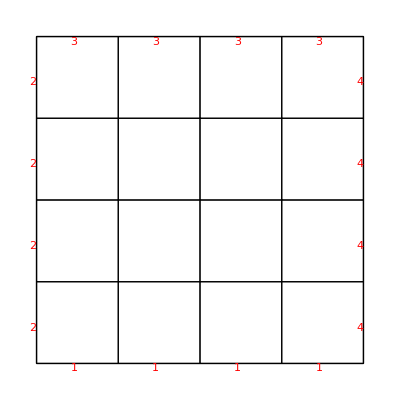

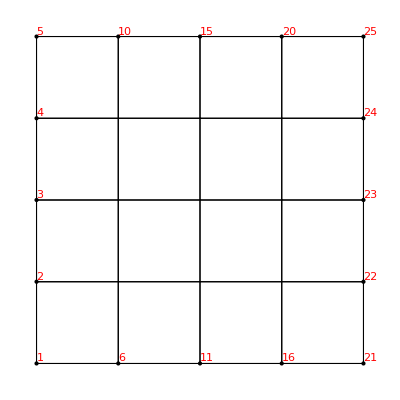

{1,6,11,16,21}

{5,10,15,20,25}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.125}

InterpolatingFunction[…]

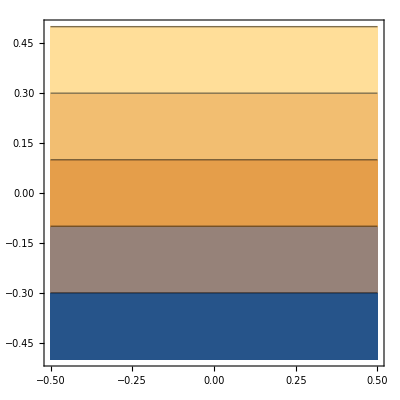

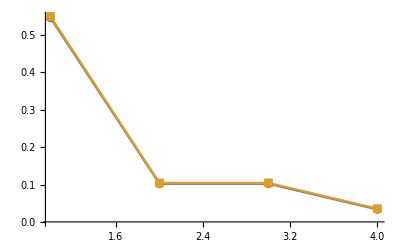

mean square error = 0.205751

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

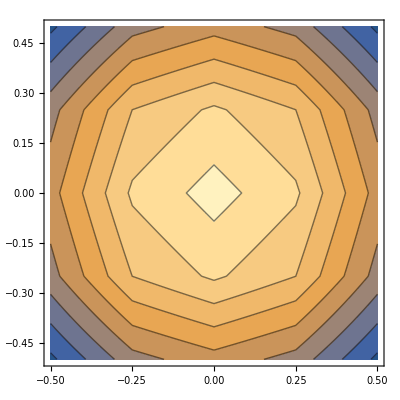

-Graphics3D-

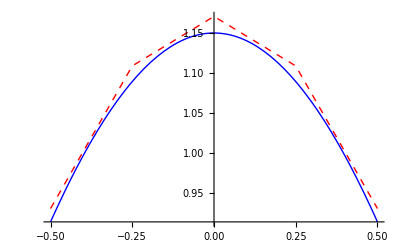

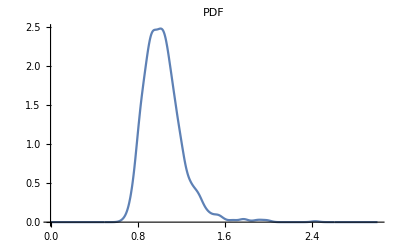
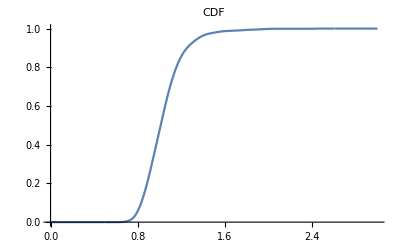

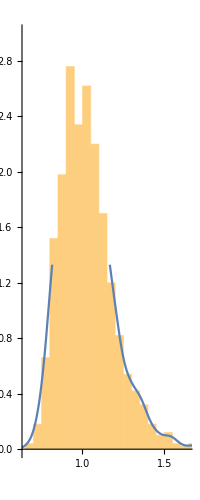

```mathematica
(*Problem 4 form section 4 of:  Ghanem,R.G.and Spanos,P.D.Stochastic Finite Element.Dover;2003. 222 p.*)
dim=2; (*Problem Dimension*)
order=1; (*Shape functions order*)
M=4;(*Karhunen-Loeve expansion terms*)
sdev=0.2 ;(*standard deviation of the random field*)
lx=1;(*Correlation length in x direction*)
ly=1;(*Correlation length in y direction*)
lz=0;(*Correlation length in z direction*)
type=2;(*Autocorrelation type*)
tick=1.;(*Thickness*)
dataautofunc={lx,ly,lz,sdev,type,dim};

m= ToElementMesh[FullRegion[2],{{-0.5,0.5},{-0.5,0.5}},"MeshOrder"->1,MaxCellMeasure->0.1];
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Directive[Red,PointSize[0.1]]]]]
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
meshnodes=m["Coordinates"];
nu=0.0;
x0=-0.5;
xf=0.5;
bodyforce={0,0};
young=1;
nu=0.;
coordstofind=Table[{x,-0.5},{x,-0.5,0.5,0.001}];
idsbottom=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]]
coordstofind=Table[{x,0.5},{x,-0.5,0.5,0.001}];
idstop=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]]
f[x_]=1.;
FG=ContributeStraigthLineNewman[meshnodes,order,idstop,{0,1},f]//N
{KG,dummy}=Assemble[m,approxfielddummy]//N;

{KG,dummy}=ContributeLineDirichlet[KG,FG,idsbottom,{1,0}];
{KG,dummy}=ContributeLineDirichlet[KG,FG,idsbottom,{2,0}];
soluu=LinearSolve[KG,FG,Method->"Banded"];
tab=Flatten[Table[Sqrt[ soluu[[i  2]]^2 +soluu[[i  2-1]]^2  ],{i, 1,Length[meshnodes] }]];
eufun=ElementMeshInterpolation[{m},tab,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}]
ContourPlot[eufun[x,y],{x,-0.5,0.5},{y,-0.5,0.5},AspectRatio->Automatic]

data={M,m};

{val,vec}=SolveGenEigenvalueProblem[data];

analyticphi={0.5458414121105973,0.10195868097200954,0.10195868097200954,0.03331186178992673};
ListLinePlot[{analyticphi,val},PlotRange->All,PlotMarkers->Automatic]
(*facs=Sqrt[Table[IntegrateSol[order,meshnodes,meshtopology,vec[[i]],vec[[i]]],{i,1,Length[vec]}]]//Chop*)
facs=Table[Sqrt[IntegrateSol[m,vec[[i]],vec[[j]]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
newvec=Table[vec[[i]]/Diagonal[facs][[i]],{i,1,Length[facs]}];
int=Table[IntegrateSol[m,newvec[[i]],newvec[[j]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
Print["mean square error = ",1- Sum[val[[i]],{i,1,M}] ]
int//Chop//MatrixForm

eufun=Table[ElementMeshInterpolation[{m},vec[[i]]/Diagonal[facs][[i]],"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}],{i,1,M}];
ContourPlot[eufun[[1]][x,y],{x,-0.5,0.5},{y,-0.5,0.5},AspectRatio->Automatic]
analytic={1.150211391123799 Cos[1.3065423741888063 x] Cos[1.3065423741888063 y],1.4217786178182625 Cos[1.3065423741888063 x] Sin[3.6731944063042516 y],1.4217786178182625 Cos[1.3065423741888063 y] Sin[3.6731944063042516 x],1.4836357792853017 Cos[6.584620042564174 x] Cos[1.3065423741888063 y]};
Plot3D[{analytic[[1]],eufun[[1]][x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->All,AxesLabel->{x,y,z}]
Plot[{analytic[[1]]/.y->0,eufun[[1]][x,0]},{x,-0.5,0.5},PlotRange->All,PlotStyle->{{Thick,Blue},{Thin,Red,Dashed}}]

A=DiagonalMatrix[Sqrt[val]].newvec;
nsamples=1000;
XI=Table[RandomVariate[NormalDistribution[0,1],nsamples],{i,1,M}];
Phi=(Transpose[A].XI);
mean=1;
sdev=0.2;
Hfield=mean+ sdev Phi;

post={};
For[imc=1,imc<=nsamples,imc++,
approxfield=Transpose[Hfield][[imc]];
{KG,dummy}=Assemble[m,approxfield]//N;
{KG,dummy}=ContributeLineDirichlet[KG,FG,idsbottom,{1,0}];
{KG,dummy}=ContributeLineDirichlet[KG,FG,idsbottom,{2,0}];
soluu=LinearSolve[KG,FG,Method->"Banded"];
sol=soluu[[FindIds[meshnodes,{0,0.5}][[1]] 2]];
If[Abs[sol]<20,
AppendTo[post,{imc,sol}];
];
];

solvec=Transpose[post][[2]];
𝒟=SmoothKernelDistribution[solvec];
Table[Plot[f[𝒟,x],{x,0.,3},PlotLabel->f,PlotRange->All],{f,{PDF,CDF}}]
Show[Histogram[solvec,Automatic,"PDF",PlotRange->{0,3}],Plot[PDF[𝒟,x],{x,0.,3}],AspectRatio->Automatic]
```

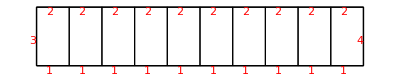

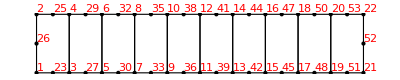

{1}

{12}

{21,52,22}

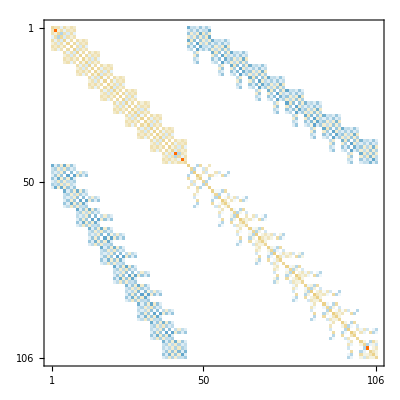

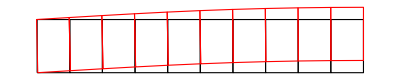

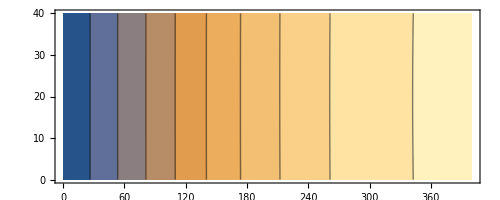

sol FEM = -9.20524

sol PTV = 9.16667

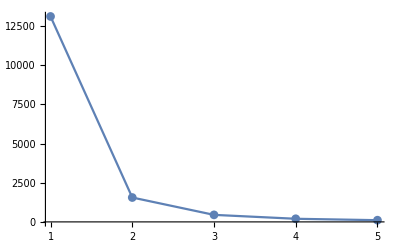

mean square error = 0.0363888

(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.)

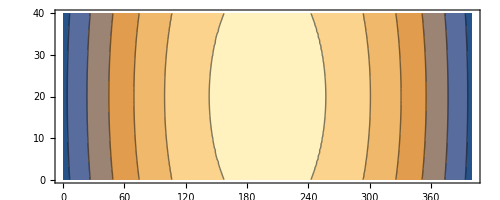

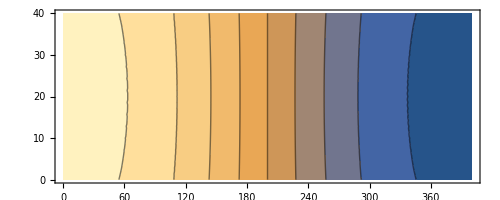

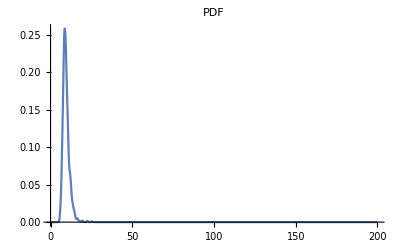
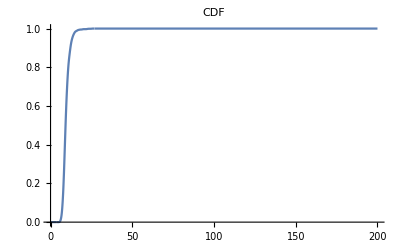

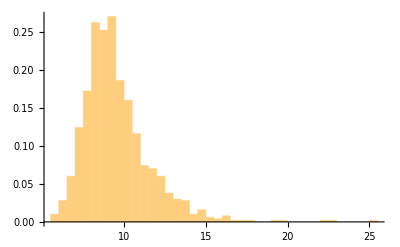

```mathematica
(*Problem 1  of:  Araújo, J.M. and Awrush, A.M. On Stochastic Finite Element for Structural Analysis (1993);2003. 222 p.*)
dim=2; (*Problem Dimension*)
order=2; (*Shape functions order*)
M=5;(*Karhunen-Loeve expansion terms*)
cov=0.2 ;(*standard deviation of the random field*)
lx=80;(*Correlation length in x direction*)
ly=8;(*Correlation length in y direction*)
lz=0;(*Correlation length in z direction*)
type=1;(*Autocorrelation type*)
h=40;
L=400;
tick=10.;(*Thickness*)
dataautofunc={lx,ly,lz,sdev,type,dim};

m= ToElementMesh[FullRegion[2],{{0,L},{0,h}},"MeshOrder"->1,MaxCellMeasure->40 40];
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Directive[Red,PointSize[0.1]]]]]
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
meshnodes=m["Coordinates"];

bodyforce={0,0};
young=305914.8638933784 ;
nu=0.2;

idleft=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,{0,0}],{i,1,Length[meshnodes]}]]]
idload=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,{L/2,h}],{i,1,Length[meshnodes]}]]]
coordsr=Table[{L,y},{y,0,h,0.01}];
idsr=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordsr[[i]]],{i,1,Length[coordsr]}]]]
{KG,FG}=Assemble[m,approxfielddummy]//N;

(*{KG,dummy}=ContributeLineDirichlet[KG,FG,idleft,{1,0}];*)
{KG,dummy}=ContributeLineDirichlet[KG,FG,idleft,{2,0}];
{KG,dummy}=ContributeLineDirichlet[KG,FG,idsr,{1,0}];
force=10197.162129779283 ;
FG[[idload 2]]=force;

soluu=LinearSolve[KG,FG,Method->"Banded"];
MatrixPlot[KG]
ufun1=Flatten[Table[soluu[[i  2-1]],{i, 1,Length[meshnodes] }]];
vfun1=Flatten[Table[soluu[[i  2]],{i, 1,Length[meshnodes] }]];
ufun=ElementMeshInterpolation[{m},ufun1,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
vfun=ElementMeshInterpolation[{m},vfun1,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
dmesh=ElementMeshDeformation[m,{ufun,vfun}];
Show[{
m["Wireframe"],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}]
ContourPlot[vfun[x,y],{x,0,L},{y,0,h},AspectRatio->Automatic]
solfem=vfun[L,0];
solptv=(1/ei Integrate[(force x)1/2 x,{x,0,L/2}]+1/ei Integrate[(force L/2)1/2 x,{x,L/2,L}] )2/.{ei->young tick h^ 3 /12.};
Print["sol FEM = ", -solfem]
Print["sol PTV = ", solptv]


data={M,m};

{val,vec}=SolveGenEigenvalueProblem[data];

ListLinePlot[val,PlotRange->All,PlotMarkers->Automatic]
(*facs=Sqrt[Table[IntegrateSol[order,meshnodes,meshtopology,vec[[i]],vec[[i]]],{i,1,Length[vec]}]]//Chop*)
facs=Table[Sqrt[IntegrateSol[m,vec[[i]],vec[[j]]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
newvec=Table[vec[[i]]/Diagonal[facs][[i]],{i,1,Length[facs]}];
int=Table[IntegrateSol[m,newvec[[i]],newvec[[j]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
Print["mean square error = ",1- Sum[val[[i]],{i,1,M}] /(h L)]
int//Chop//MatrixForm

eufun=Table[ElementMeshInterpolation[{m},vec[[i]]/Diagonal[facs][[i]],"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}],{i,1,M}];
ContourPlot[eufun[[1]][x,y],{x,0,L},{y,0,h},AspectRatio->Automatic]
ContourPlot[eufun[[2]][x,y],{x,0,L},{y,0,h},AspectRatio->Automatic]

A=DiagonalMatrix[Sqrt[val]].newvec;
nsamples=1000;
XI=Table[RandomVariate[NormalDistribution[0,1],nsamples],{i,1,M}];
Phi=(Transpose[A].XI);
mean=young;
sdev=cov young;
Hfield=mean+ sdev Phi;

post={};
For[imc=1,imc<=nsamples,imc++,
approxfield=Transpose[Hfield][[imc]];
{KG,dummy}=Assemble[m,approxfield]//N;
{KG,dummy}=ContributeLineDirichlet[KG,FG,idleft,{2,0}];
{KG,dummy}=ContributeLineDirichlet[KG,FG,idsr,{1,0}];
FG[[idload 2]]=-force;
soluu=LinearSolve[KG,FG,Method->"Banded"];
sol=soluu[[FindIds[meshnodes,{L,0}][[1]] 2]];
AppendTo[post,{imc,Abs[sol]}];

];

solvec=Transpose[post][[2]];
𝒟=SmoothKernelDistribution[solvec];
Table[Plot[f[𝒟,x],{x,0.,L/2},PlotLabel->f,PlotRange->All],{f,{PDF,CDF}}]
Show[Histogram[solvec,Automatic,"PDF",PlotRange->All]]
```

```mathematica
force
```

10197.2

-Graphics3D-

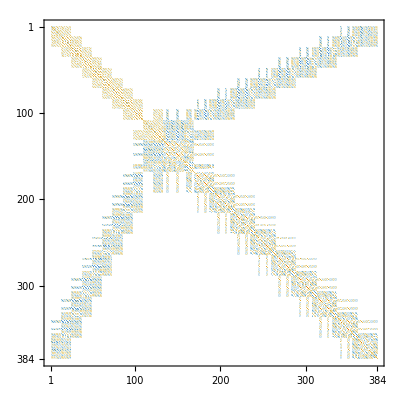

21

23

-Graphics3D-

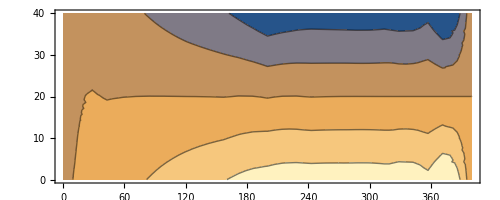

sol FEM = -9.19468

val(131022.
15526.3
4464.75
1971.23
1070.49)

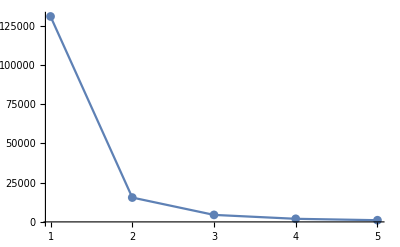

mean square error = 0.0371549

(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.)

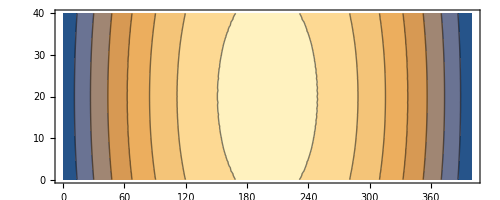

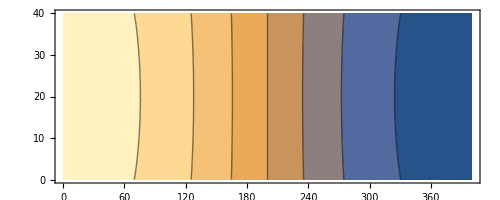

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

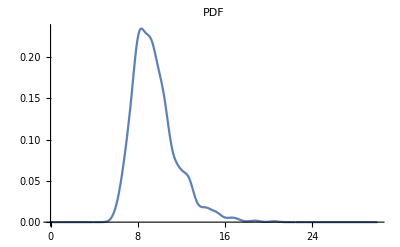
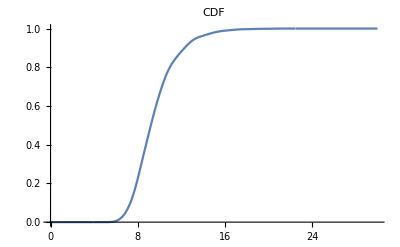

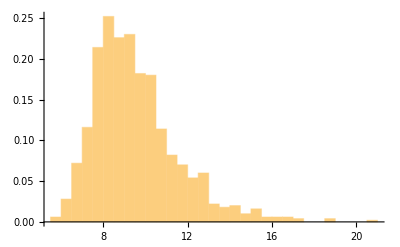

```mathematica
(*Problem 1  of:  Araújo, J.M. and Awrush, A.M. On Stochastic Finite Element for Structural Analysis (1993);2003. 222 p.*)
dim=3; (*Problem Dimension*)
order=2; (*Shape functions order*)
M=5;(*Karhunen-Loeve expansion terms*)
sdev=0.2 ;(*standard deviation of the random field*)
lx=80;(*Correlation length in x direction*)
ly=8;(*Correlation length in y direction*)
lz=8;(*Correlation length in z direction*)
type=1;(*Autocorrelation type*)
tick=10.;(*Thickness*)
dataautofunc={lx,ly,lz,sdev,type,dim};
L=400;
b=10.;
h=40;
bodyforce={0,0,0};
m=ToElementMesh[FullRegion[3],{{0,L},{0,b},{0,h}},"MeshOrder"->order,MaxCellMeasure->L b h/2,"NodeReordering"->True];
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementStyle"->Directive[Red,PointSize[0.012]]]]]
meshnodes=m["Coordinates"];

young=305914.8638933784 ;
nu=0.2;

{ke,fe}=Assemble[m,order];
MatrixPlot[ke]

coordstofind=Table[{0,y,0},{y,0,b,0.1}];
idsleft=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];
dir=3;
val=0;
{ke2,fe2}=ContributeLineDirichlet[ke,fe,idsleft,{dir,val}];

coordstofind=Flatten[Table[{L,y,z},{y,0,b,0.1},{z,0,h,0.1}],1];
idsrigth=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]];

dir=2;
val=0;
{ke2,fe2}=ContributeLineDirichlet[ke2,fe2,idsrigth,{dir,val}];
dir=1;
{ke2,fe2}=ContributeLineDirichlet[ke2,fe2,idsrigth,{dir,val}];

loadid1=FindIds[meshnodes,{L/2,0,h}][[1]]
loadid2=FindIds[meshnodes,{L/2,b,h}][[1]]
fe2[[ loadid1 3]]=-10197.162129779283/2;
fe2[[ loadid2 3]]=-10197.162129779283/2;

soluu=LinearSolve[ke2,fe2,Method->"Cholesky"];
ufun1=Flatten[Table[soluu[[i  3-2]],{i, 1,Length[meshnodes] }]];
vfun1=Flatten[Table[soluu[[i  3-1]],{i, 1,Length[meshnodes] }]];
wfun1=Flatten[Table[soluu[[i  3]],{i, 1,Length[meshnodes] }]];
ufun=ElementMeshInterpolation[{m},ufun1,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
vfun=ElementMeshInterpolation[{m},vfun1,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
wfun=ElementMeshInterpolation[{m},wfun1,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
dmesh=ElementMeshDeformation[m,{ufun,vfun,wfun}];
Show[{
m["Wireframe"],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}]
ContourPlot[vfun[x,0,z],{x,0,L},{z,0,h},AspectRatio->Automatic]
solfem=wfun[L,0,0];
Print["sol FEM = ", solfem]


data={M,m};

{val,vec}=SolveGenEigenvalueProblem[data];
Print["val", val//MatrixForm];

ListLinePlot[val,PlotRange->All,PlotMarkers->Automatic]
(*facs=Sqrt[Table[IntegrateSol[order,meshnodes,meshtopology,vec[[i]],vec[[i]]],{i,1,Length[vec]}]]//Chop*)
facs=Table[Sqrt[IntegrateSol[m,vec[[i]],vec[[j]]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
newvec=Table[vec[[i]]/Diagonal[facs][[i]],{i,1,Length[facs]}];
int=Table[IntegrateSol[m,newvec[[i]],newvec[[j]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
Print["mean square error = ",1- Sum[val[[i]],{i,1,M}] /(h L b)]
int//Chop//MatrixForm

eufun=Table[ElementMeshInterpolation[{m},vec[[i]]/Diagonal[facs][[i]],"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}],{i,1,M}];
ContourPlot[eufun[[1]][x,0,z],{x,0,L},{z,0,h},AspectRatio->Automatic]
ContourPlot[eufun[[2]][x,0,z],{x,0,L},{z,0,h},AspectRatio->Automatic]
Table[Legended[ElementMeshSurfacePlot3D[vec[[i]],m,ViewPoint->{0,-4,2},Axes->True,AxesLabel->{X,Y,Z}],BarLegend[{ColorFunction/.Options[ElementMeshSurfacePlot3D]//First,{Min[vec[[i]]],Max[vec[[i]]]}}]],{i,1,3}]


A=DiagonalMatrix[Sqrt[val]].newvec;
nsamples=1000;
XI=Table[RandomVariate[NormalDistribution[0,1],nsamples],{i,1,M}];
Phi=(Transpose[A].XI);
mean=young;
sdev=0.2 young;
Hfield=mean+ sdev Phi;


post={};
For[imc=1,imc<=nsamples,imc++,

approxfield=Transpose[Hfield][[imc]];

{ke,fe}=Assemble[m,approxfield]//N;
dir=3;
val=0;
{ke2,fe2}=ContributeLineDirichlet[ke,fe,idsleft,{dir,val}];
dir=2;
val=0;
{ke2,fe2}=ContributeLineDirichlet[ke2,fe2,idsrigth,{dir,val}];
dir=1;
{ke2,fe2}=ContributeLineDirichlet[ke2,fe2,idsrigth,{dir,val}];
fe2[[ loadid1 3]]=-10197.162129779283/2;
fe2[[ loadid2 3]]=-10197.162129779283/2;
soluu=LinearSolve[ke2,fe2,Method->"Banded"];
sol=soluu[[FindIds[meshnodes,{L,0,0}][[1]] 3]];
AppendTo[post,{imc,Abs[sol]}];

];

solvec=Transpose[post][[2]];
𝒟=SmoothKernelDistribution[solvec];
Table[Plot[f[𝒟,x],{x,0.,30},PlotLabel->f,PlotRange->All],{f,{PDF,CDF}}]
Show[Histogram[solvec,Automatic,"PDF",PlotRange->All]]
```

ElementMesh[{{3.67394×10^-17,1.},{0.,1.}},{QuadElement[<57>]}]

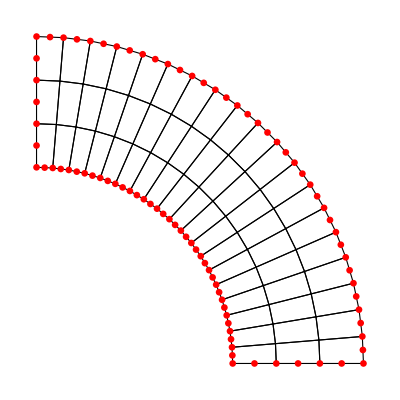

val(0.238125
0.0908916
0.0358711
0.0175159
0.0156805
0.0117732
0.00991265
0.00809574
0.00642379
0.00483126)

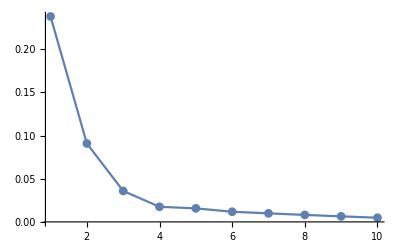

mean square error = 1-0.439121/(b h L)

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
<<NDSolve`FEM`
(*PROBLEM  FROM SECTION 4 OF REFERENCE 4*)
dim=2; (*Problem Dimension*)
order=2; (*Shape functions order*)
M=10;(*Karhunen-Loeve expansion terms*)
sdev=1 ;(*standard deviation of the random field*)
lx=1;(*Correlation length in x direction*)
ly=0.5;(*Correlation length in y direction*)
lz=0;(*Correlation length in z direction*)
type=2;(*Autocorrelation type*)
dataautofunc={lx,ly,lz,sdev,type,dim};
re=1;
ri=0.6;
nx=20;
ny=4;
coordinates=Flatten[ Table[{r Cos[θ], r Sin[θ]}, {r, ri,re,(re-ri)/(ny-1)}, {θ, 0.,  Pi/2.,( Pi/2.)/(nx-1)}], 1];
incidents=Flatten[Table[{j*nx+i,j*nx+i+1,(j-1)*nx+i+1,(j-1)*nx+i},{i,1,nx-1},{j,1,ny-1}],1];
m=ToElementMesh["Coordinates"->coordinates,"MeshElements"->{QuadElement[incidents]}]
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementStyle"->Directive[Red,PointSize[0.012]]]]]

data={M,m};

{val,vec}=SolveGenEigenvalueProblem[data];
Print["val", val//MatrixForm];

ListLinePlot[val,PlotRange->All,PlotMarkers->Automatic]
(*facs=Sqrt[Table[IntegrateSol[order,meshnodes,meshtopology,vec[[i]],vec[[i]]],{i,1,Length[vec]}]]//Chop*)
facs=Table[Sqrt[IntegrateSol[m,vec[[i]],vec[[j]]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
newvec=Table[vec[[i]]/Diagonal[facs][[i]],{i,1,Length[facs]}];
int=Table[IntegrateSol[m,newvec[[i]],newvec[[j]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
Print["mean square error = ",1- Sum[val[[i]],{i,1,M}] /(h L b)]
int//Chop//MatrixForm
```

-Graphics3D-

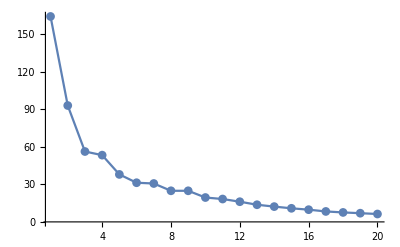

mean square error = 0.23932

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
<<NDSolve`FEM`
dim=3; (*dimension*)
order=2; (*shape order*)
M=20;(*KLE expansion terms*)
sdev=1 ;(*standard deviation*)
lx=10.;(*autocorrelation length in x*)
ly=0.5;(*autocorrelation length in y*)
lz=0.0;(*autocorrelation length in z*)
type=1;(*autocorrelation type*)
dataautofunc={lx,ly,lz,sdev,type,dim};
nx=32/4;ny=4/2 ;nz=8/4;
H=15;
re=10;
ri=8;
coordinates=Flatten[ Table[{r Cos[θ], r Sin[θ], h},{h, 0,H,H/(nz-1)}, {r,ri,re,(re-ri)/(ny-1)}, {θ, 0., Pi,( Pi)/(nx-1)}], 2];
incidents=Flatten[Table[Block[{p1=(j-1)*nx+i,p2=j*nx+i,p3=p2+1,p4=p1+1,p5,p6,p7,p8},
{p5,p6,p7,p8}={p1,p2,p3,p4}+k*nx*ny;
{p1,p2,p3,p4}+=(k-1)*nx*ny;
{p1,p2,p3,p4,p5,p6,p7,p8}],{i,1,nx-1},{j,1,ny-1},{k,1,nz-1}],2];
m=ToElementMesh["Coordinates"->coordinates,"MeshElements"->{HexahedronElement[incidents]},"NodeReordering"->True];
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementStyle"->Directive[Red,PointSize[0.012]]]]]

data={M,m};
{time,{val,vec}}=Timing[SolveGenEigenvalueProblem[data]];

ListLinePlot[val,PlotRange->All,PlotMarkers->Automatic]
(*facs=Sqrt[Table[IntegrateSol[order,meshnodes,meshtopology,vec[[i]],vec[[i]]],{i,1,Length[vec]}]]//Chop*)
facs=Table[Sqrt[IntegrateSol[m,vec[[i]],vec[[j]]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
newvec=Table[vec[[i]]/Diagonal[facs][[i]],{i,1,Length[facs]}];
int=Table[IntegrateSol[m,newvec[[i]],newvec[[j]]],{i,1,Length[vec]},{j,1,Length[vec]}]//Chop;
Print["mean square error = ",1- Sum[val[[i]],{i,1,M}] /(Pi/8 (20^2 - 16^2)15)]
int//Chop//MatrixForm

eufun=Table[ElementMeshInterpolation[{m},vec[[i]]/Diagonal[facs][[i]],"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}],{i,1,M}];
Table[Legended[ElementMeshSurfacePlot3D[vec[[i]],m,ViewPoint->{0,-4,2},Axes->True,AxesLabel->{X,Y,Z}],BarLegend[{ColorFunction/.Options[ElementMeshSurfacePlot3D]//First,{Min[vec[[i]]],Max[vec[[i]]]}}]],{i,1,3}]
```

```mathematica
time
```

31.1045

```mathematica
time
```

31.1045